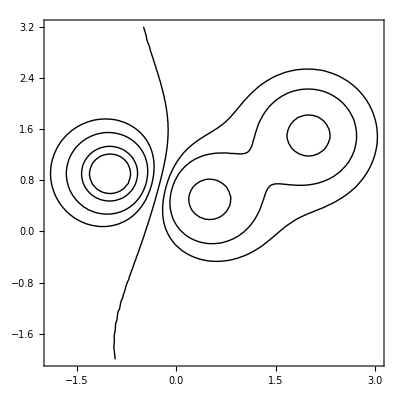

```mathematica
q1 = 1/((x+1)^2+(y-0.9)^2);
q2=1/((x-0.5)^2+(y-0.5)^2);
q3=1/((x-2)^2+(y-1.5)^2);
ContourPlot[-q1+q2+q3,{x,-2.5,5.5},{y,-2,3.2},Contours->{-10,-5,-2,-1,0.05,1,2,10},PlotRange->All,ContourShading->None]
```

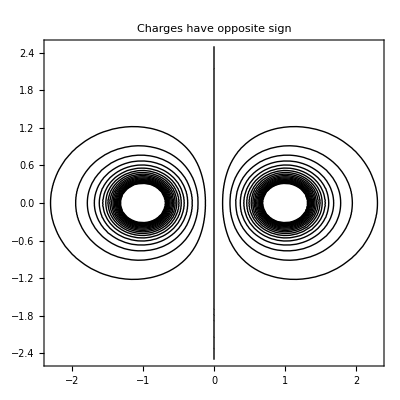

```mathematica
q1 = 1/((x+1)^2+(y)^2);
q2 = 1/((x-1)^2+(y)^2);
ContourPlot[-q1+q2,{x,-5,5},{y,-2.5,2.5},Contours->Range[-10,10,0.5],PlotRange->All,ContourShading->None,PlotLabel->"Charges have opposite sign"]
```

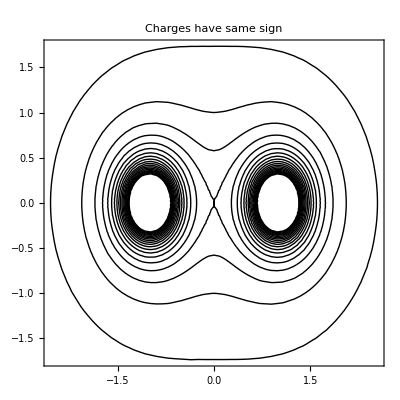

```mathematica
ContourPlot[q1+q2,{x,-5,5},{y,-2.5,2.5},Contours->Range[-10,10,0.5],PlotRange->All,ContourShading->None,PlotLabel->"Charges have same sign"]
```